# Making Graphs

## Plot

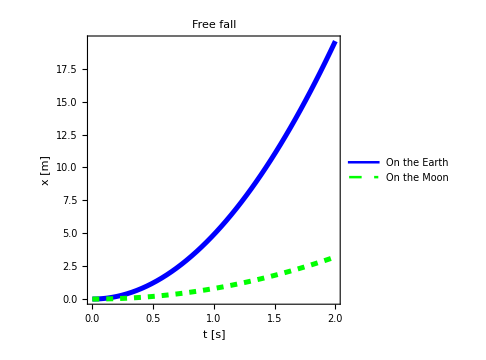

```mathematica
f[t_]=(9.8/2)*t^2;(*Free fall on the Earth*)
g[t_]=(1.6/2)*t^2;(*Free fall on the Moon*)

Plot[{f[t],g[t]},{t,0,2},
PlotLegends->Placed[{Style["On the Earth",FontSize->18,Black,FontFamily->"Times New Roman"],Style["On the Moon",FontSize->18,Black,FontFamily->"Times New Roman"]},Right],
PlotStyle->{Directive[Blue,Thickness[0.01]],{Green,Thickness[0.01],Dashed}},
PlotRange->{{0,2},{f[0],f[2]}},
PlotLabel->Style["Free fall",Bold,FontSize->20,Black,FontFamily->"Times New Roman"],
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Black],
FrameLabel->{Row[{Style["t",Italic,FontSize->20,Black,FontFamily->"Times New Roman"],Style[" [s]",FontSize->20,Black,FontFamily->"Times New Roman"]}],Row[{Style["x",Italic,FontSize->20,Black,FontFamily->"Times New Roman"],Style[" [m]",FontSize->20,Black,FontFamily->"Times New Roman"]}]},
FrameTicksStyle->Directive[Black,FontSize->20,  FontFamily->"Times New Roman"],
ImageSize->Medium]
```

# Version Number

```mathematica
$VersionNumber
```

11.